## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=2.5; Q=0.99;
```

```mathematica
winit=(0.3-0.0001*I)
```

0.3-0.0001 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.301538+0.000180599 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

2.16902

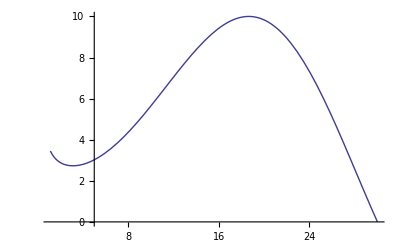

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.3-0.0001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.3-0.0001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{30.,0.301538},{29.8,0.30312},{29.6,0.304724},{29.4,0.306351},{29.2,0.308},{29.,0.309672},{28.8,0.311369},{28.6,0.313089},{28.4,0.314834},{28.2,0.316605},{28.,0.318401},{27.8,0.320224},{27.6,0.322073},{27.4,0.32395},{27.2,0.325855},{27.,0.327789},{26.8,0.329752},{26.6,0.331744},{26.4,0.333768},{26.2,0.335822},{26.,0.337908},{25.8,0.340028},{25.6,0.34218},{25.4,0.344366},{25.2,0.346588},{25.,0.348845},{24.8,0.351138},{24.6,0.353469},{24.4,0.355839},{24.2,0.358247},{24.,0.360696},{23.8,0.363185},{23.6,0.365717},{23.4,0.368291},{23.2,0.37091},{23.,0.373574},{22.8,0.376285},{22.6,0.379042},{22.4,0.381849},{22.2,0.384706},{22.,0.387614},{21.8,0.390574},{21.6,0.393588},{21.4,0.396658},{21.2,0.399785},{21.,0.40297},{20.8,0.406215},{20.6,0.409522},{20.4,0.412892},{20.2,0.416327},{20.,0.419829},{19.8,0.4234},{19.6,0.427042},{19.4,0.430756},{19.2,0.434546},{19.,0.438412},{18.8,0.442358},{18.6,0.446386},{18.4,0.450498},{18.2,0.454697},{18.,0.458985},{17.8,0.463366},{17.6,0.467841},{17.4,0.472415},{17.2,0.477091},{17.,0.481871},{16.8,0.486759},{16.6,0.491759},{16.4,0.496874},{16.2,0.502109},{16.,0.507466},{15.8,0.512952},{15.6,0.518569},{15.4,0.524323},{15.2,0.530219},{15.,0.536262},{14.8,0.542457},{14.6,0.548809},{14.4,0.555325},{14.2,0.562011},{14.,0.568873},{13.8,0.575918},{13.6,0.583153},{13.4,0.590587},{13.2,0.598226},{13.,0.606079},{12.8,0.614156},{12.6,0.622465},{12.4,0.631016},{12.2,0.63982},{12.,0.648888},{11.8,0.658231},{11.6,0.667861},{11.4,0.677793},{11.2,0.688039},{11.,0.698614},{10.8,0.709535},{10.6,0.720816},{10.4,0.732477},{10.2,0.744536},{10.,0.757013}}

```mathematica
winit=(0.8-0.0001*I);
ie=0;While[ie<41,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=10-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,40}];
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,40}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

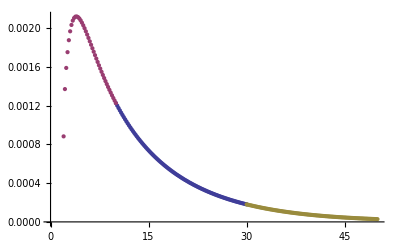

```mathematica
ListPlot[{t2l,t2l2,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

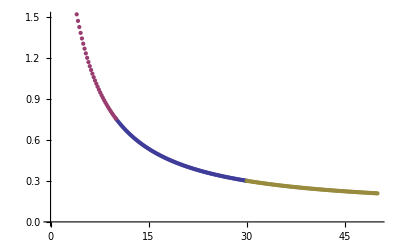

```mathematica
ListPlot[{t1l,t1l2,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=2.5/R.dat",Join[t1l,t1l2,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=2.5/I.dat",Join[t2l,t2l2,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=2.5/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=2.5/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```